```mathematica
Get["C:\\Users\\jacks\\Documents\\GitHub\\cdt_rust\\Mathematica\\CDTFunctions.wl"]
```

```mathematica
groundTruth = VPCounts[14,3];
groundTruth=KeySortBy[groundTruth,groundTruth[#]&];
groundTruthNorm=groundTruth/Total[groundTruth];
order = Keys[groundTruth];
```

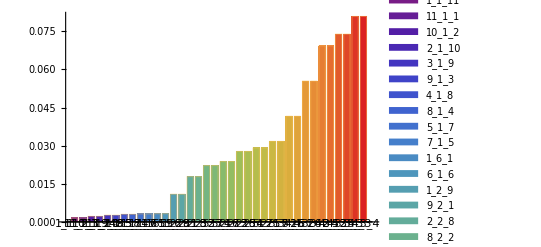

```mathematica
BarChart[Tooltip[groundTruthNorm,Keys[groundTruthNorm]],ChartLabels->Automatic,ChartStyle->"Rainbow",ChartLegends->Placed[Automatic,Below],RotateLabel->True]
```

```mathematica
folder="C:\\Users\\jacks\\Documents\\GitHub\\cdt_rust\\data";
files=FileNames["Statistical_Volume_14_TimeSize_3*.csv",folder];
vpData = LoadVPData[files];
```

```mathematica
vpCountsNormed =Association[Table[stepCount-> Table[SortNormCounts[Counts[vpData[stepCount][[index]]],order],{index,Length[vpData[stepCount]]}],{stepCount,Keys[vpData]}]];
```

```mathematica
vpCounts =Association[Table[stepCount-> Table[SortCounts[Counts[vpData[stepCount][[index]]],order],{index,Length[vpData[stepCount]]}],{stepCount,Keys[vpData]}]];
```

```mathematica
vpCountsScaled =Association[Table[stepCount-> Table[Total[groundTruth]SortNormCounts[Counts[vpData[stepCount][[index]]],order],{index,Length[vpData[stepCount]]}],{stepCount,Keys[vpData]}]];
```

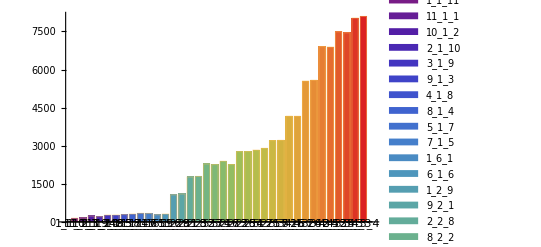

```mathematica
BarChart[Counts[vpData[10][[1]]][[order]],ChartLabels->Automatic,ChartStyle->"Rainbow",ChartLegends->Placed[Automatic,Below],RotateLabel->True]
```

```mathematica
residuals = Table[(vpcounts-groundTruthNorm)/groundTruthNorm,{vpcounts,vpCountsNormed[10]}];
```

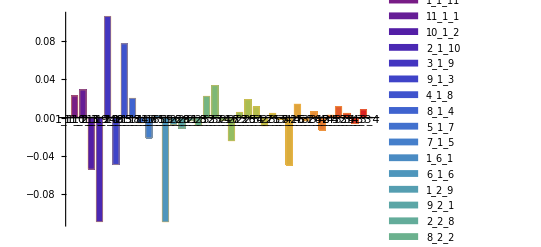

```mathematica
BarChart[residuals[[2]],ChartLabels->Automatic,ChartStyle->"Rainbow",ChartLegends->Placed[Automatic,Below],RotateLabel->True]
```

```mathematica
combinedresiduals=Merge[residuals,Join];
```

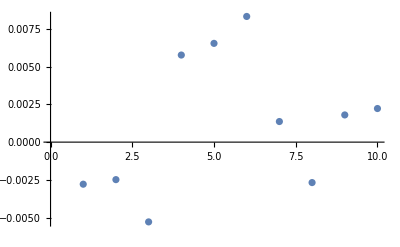

```mathematica
ListPlot[Mean[combinedresiduals]]
```

```mathematica
Table[i,{i,-1,1,.1}]
```

{-1.,-0.9,-0.8,-0.7,-0.6,-0.5,-0.4,-0.3,-0.2,-0.1,0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}

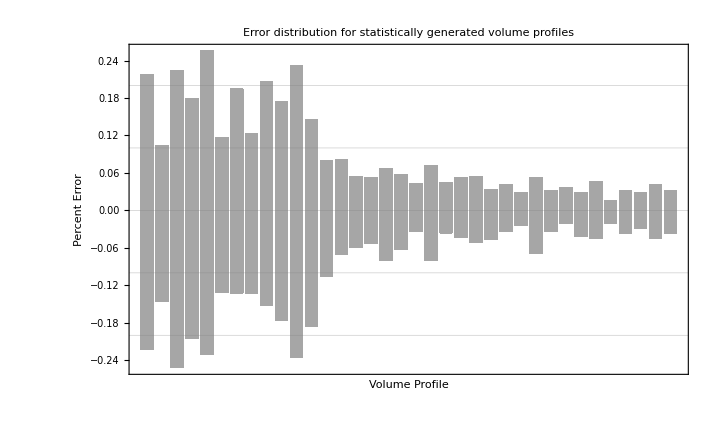

```mathematica
DistributionChart[combinedresiduals,ChartElementFunction->"Density",ChartBaseStyle->EdgeForm[],Frame->{{True,False},{False,False}},AxesLabel->{"Volume Profile","Percent Error"},PlotLabel->"Error distribution for statistically generated volume profiles",GridLines->{{}, Table[i,{i,-1,1,.1}]}]
```